Practical 2

Particular solutions of the non - homogenous equation

```mathematica
Sol=DSolve[y''[x]+5*y'[x]-6*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-6 x) C[1]+ⅇ^x C[2]}}

```mathematica
Sol1=y[x]/.Sol[[1]]/.{C[1]-> 2,C[2]-> 7}
```

2 ⅇ^(-6 x)+7 ⅇ^x

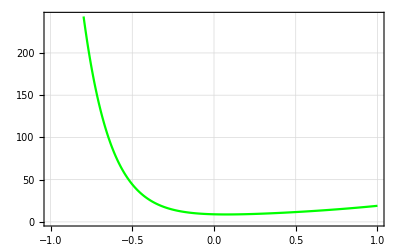

```mathematica
Plot[{Sol1},{x,-1,1},PlotStyle-> {Green},
Frame-> True,AxesOrigin-> {0,0},GridLines-> Automatic]
```

```mathematica
Sol=DSolve[y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

{Cos[x]+2 Sin[x]}

{Cos[x]+3 Sin[x]}

{Cos[x]+4 Sin[x]}

{Cos[x]+5 Sin[x]}

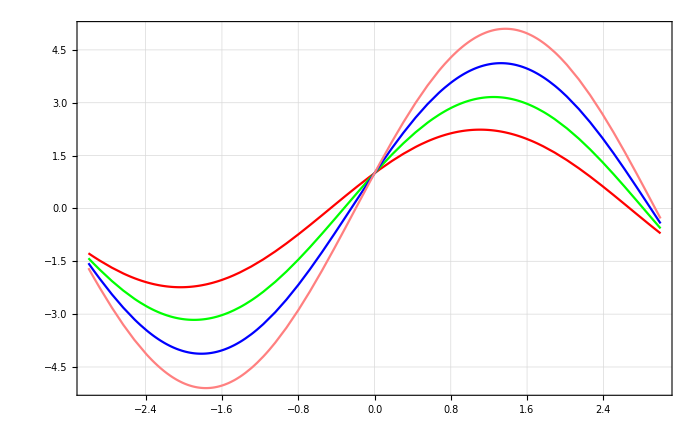

```mathematica
Sol1=y[x]/.Sol/.{C[1]-> 1,C[2]-> 2}
Sol2=y[x]/.Sol/.{C[1]-> 1,C[2]-> 3}
Sol3=y[x]/.Sol/.{C[1]-> 1,C[2]-> 4}
Sol4=y[x]/.Sol/.{C[1]-> 1,C[2]-> 5}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},
Frame-> True,AxesOrigin->{0,0},GridLines->Automatic,ImageSize->700,
PlotLegends->LineLegend[{"Sol1","Sol2","Sol3","Sol4"},LegendFunction->"Frame"]]
```

```mathematica
Sol2=DSolve[y''[x]-6*y'[x]+9y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(3 x) C[1]+ⅇ^(3 x) x C[2]}}

2 ⅇ^(3 x)+3 ⅇ^(3 x) x

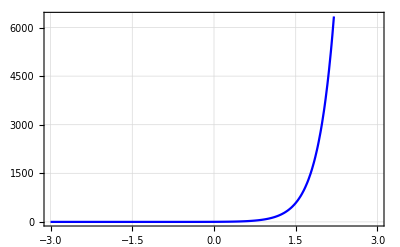

```mathematica
Sol3=y[x]/.Sol2[[1]]/.{C[1]-> 2,C[2]-> 3}
Plot[{Sol3},{x,-3,3},PlotStyle-> {Blue},
Frame-> True,AxesOrigin-> {0,0},GridLines-> Automatic]
```

```mathematica
Sol2=DSolve[y''[x]-6*y'[x]+9y[x]==0,y[x],x]
Sol3=y[x]/.Sol2[[1]]/.{C[1]-> 2,C[2]-> 3}
Plot[{Sol3},{x,-3,3},PlotStyle-> {Blue},
Frame-> True,AxesOrigin-> {0,0},GridLines-> Automatic]
```

{{y[x]→ⅇ^(3 x) C[1]+ⅇ^(3 x) x C[2]}}

2 ⅇ^(3 x)+3 ⅇ^(3 x) x

-Graphics-

```mathematica
B=DSolve[4y''[x]+12y'[x]+9y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-3 x/2) C[1]+ⅇ^(-3 x/2) x C[2]}}

```mathematica
B1=Table[y[x]/.B/.{C[1]-> 1,C[2]-> K},{K,2,5}]
```

{{ⅇ^(-3 x/2)+2 ⅇ^(-3 x/2) x},{ⅇ^(-3 x/2)+3 ⅇ^(-3 x/2) x},{ⅇ^(-3 x/2)+4 ⅇ^(-3 x/2) x},{ⅇ^(-3 x/2)+5 ⅇ^(-3 x/2) x}}

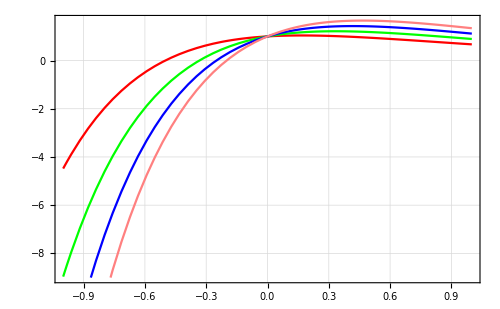

```mathematica
Plot[B1,{x,-1,1},PlotStyle->{Red,Green,Blue,Pink},
GridLines-> Automatic,Frame-> True,AxesOrigin->{0,0},ImageSize->500,
PlotLegends->LineLegend[{"Sol1","Sol2","Sol3","Sol4"},LegendFunction->"Frame"]]
```

```mathematica
Sol4=DSolve[y''[x]-y'[x]+y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}

```mathematica
{{y[x]->ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}
{{y[x]->ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}
```

{{y[x]→ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}

{{y[x]→ⅇ^(x/2) C[1] Cos[(√3 x)/2]+ⅇ^(x/2) C[2] Sin[(√3 x)/2]}}

```mathematica
Sol5=y[x]/.Sol4[[1]]/.{C[1]-> 2,C[2]-> 3}
```

2 ⅇ^(x/2) Cos[(√3 x)/2]+3 ⅇ^(x/2) Sin[(√3 x)/2]

```mathematica
2 ⅇ^(x/2) Cos[(√3 x)/2]+3 ⅇ^(x/2) Sin[(√3 x)/2]
```

2 ⅇ^(x/2) Cos[(√3 x)/2]+3 ⅇ^(x/2) Sin[(√3 x)/2]

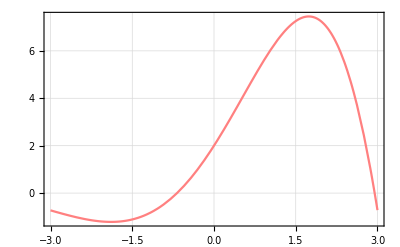

```mathematica
Plot[{Sol5},{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},
Frame-> True,AxesOrigin-> {0,0},GridLines-> Automatic]
```

```mathematica
c=DSolve[y''[x]-4*y'[x]+13*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(2 x) C[2] Cos[3 x]+ⅇ^(2 x) C[1] Sin[3 x]}}

```mathematica
c1=Table[y[x]/.c/.{C[1]-> K,C[2]-> 2},{K,3,6}]
```

{{2 ⅇ^(2 x) Cos[3 x]+3 ⅇ^(2 x) Sin[3 x]},{2 ⅇ^(2 x) Cos[3 x]+4 ⅇ^(2 x) Sin[3 x]},{2 ⅇ^(2 x) Cos[3 x]+5 ⅇ^(2 x) Sin[3 x]},{2 ⅇ^(2 x) Cos[3 x]+6 ⅇ^(2 x) Sin[3 x]}}

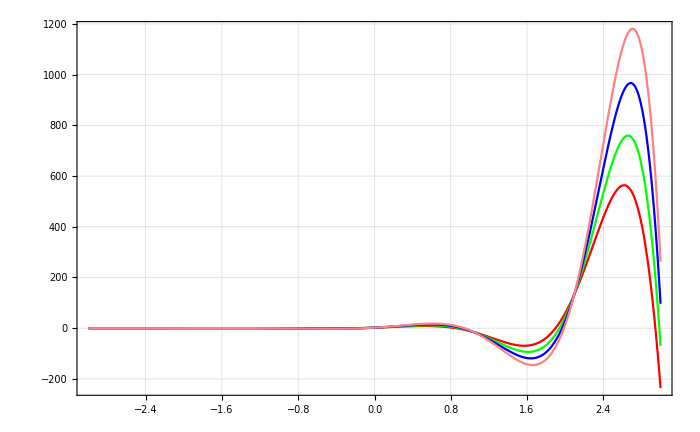

```mathematica
Plot[{c1},{x,-3,3},PlotStyle-> {Red,Green,Blue,Pink},GridLines-> Automatic,
Frame-> True,AxesOrigin-> {0,0},PlotRange-> All,ImageSize->700]
```

```mathematica
p=DSolve[{y''[x]+y'[x]-2*y[x]==0,y[0]==4,y'[0]==-5},y[x],x]
```

{{y[x]→ⅇ^(-2 x) (3+ⅇ^(3 x))}}

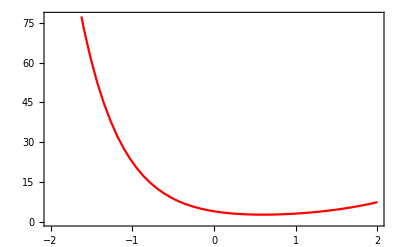

```mathematica
Plot[y[x]/.p,{x,-2,2},PlotStyle-> {Red},Frame-> True]
```

```mathematica
r=DSolve[y''[x]-2*y'[x]-3*y[x]==30*Exp[2*x],y[x],x]
```

{{y[x]→-10 ⅇ^(2 x)+ⅇ^-x C[1]+ⅇ^(3 x) C[2]}}

```mathematica
a=Table[y[x]/.r/.{C[1]-> K,C[2]-> 2},{K,3,6}]
```

{{3 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)},{4 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)},{5 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)},{6 ⅇ^-x-10 ⅇ^(2 x)+2 ⅇ^(3 x)}}

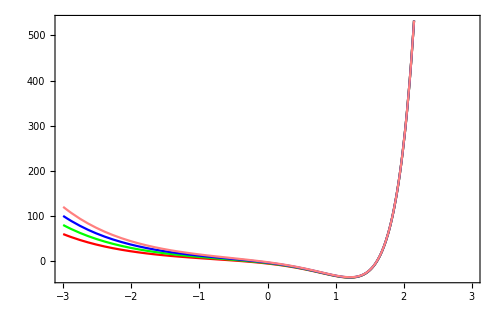

```mathematica
Plot[{a},{x,-3,3},PlotStyle-> {Red,Green,Blue,Pink},
ImageSize-> 500,Frame->True,AxesOrigin-> {0,0}]
```

```mathematica
p=DSolve[y''[x]-2*y'[x]-3*y[x]==2*Sin[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+1/5 (Cos[x]-2 Sin[x])}}

```mathematica
p1=Table[y[x]/.p/.{C[1]-> m,C[2]-> m},{m,4,7}]
```

{{4 ⅇ^-x+4 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{5 ⅇ^-x+5 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{6 ⅇ^-x+6 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{7 ⅇ^-x+7 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])}}

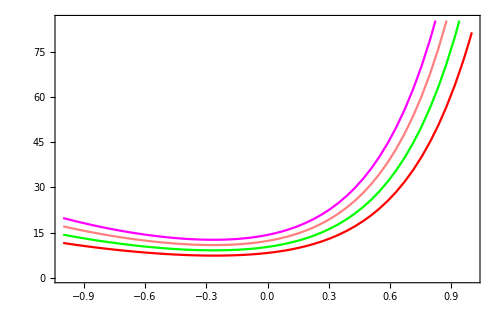

```mathematica
Plot[{p1},{x,-1,1},PlotStyle-> {Red,Green,Pink, Magenta},
Frame-> True,ImageSize-> 500,AxesOrigin-> {0,0}]
```

```mathematica
p2=Table[y[x]/.p/.{C[1]->1,C[2]->m},{m,4,7}]
```

{{ⅇ^-x+4 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{ⅇ^-x+5 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{ⅇ^-x+6 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{ⅇ^-x+7 ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])}}

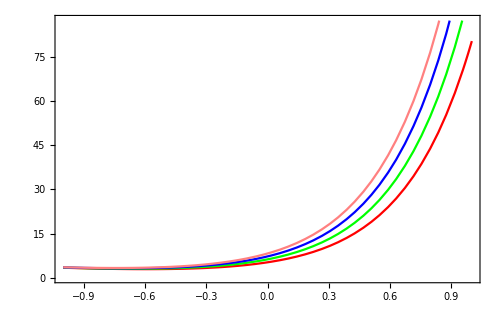

```mathematica
Plot[{p2},{x,-1,1},PlotStyle-> {Red,Green,Blue,Pink},
Frame-> True,ImageSize-> 500,AxesOrigin-> {0,0}]
```

```mathematica
p3=Table[y[x]/.p/.{C[1]->m,C[2]->1},{m,4,7}]
```

{{4 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{5 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{6 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])},{7 ⅇ^-x+ⅇ^(3 x)+1/5 (Cos[x]-2 Sin[x])}}

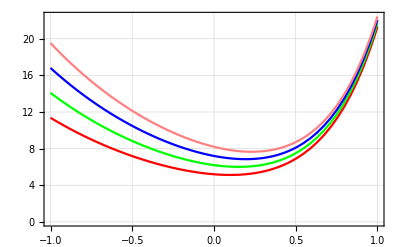

```mathematica
Plot[{p3},{x,-1,1},PlotStyle-> {Red,Green,Blue,Pink},
GridLines->Automatic,Frame-> True,AxesOrigin-> {0,0}]
```

```mathematica
q2=DSolve[{y''[x]+y[x]==.001*x^2,y[0]==0,y'[0]==1.5},y[x],x]
```

{{y[x]→-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]}}

```mathematica
q3=Table[y[x]/.q2[[1]]]
```

-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]

{-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]}

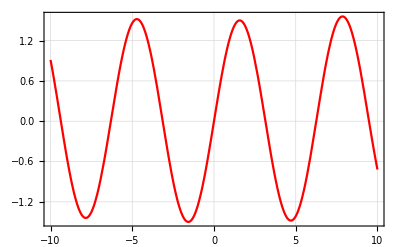

```mathematica
{-0.002+0.001 x^2+0.002 Cos[1. x]+1.5 Sin[1. x]}
Plot[q3,{x,-10,10},PlotStyle-> {Red},
GridLines->Automatic,Frame-> True,AxesOrigin-> {0,0},PlotLegends->Automatic]
```

```mathematica
b=DSolve[x^2*y''[x]-2*x*y'[x]-4*y[x]==0,y[x],x]
```

{{y[x]→C[1]/x+x^4 C[2]}}

```mathematica
c=Table[y[x]/.b/.{C[1]->K,C[2]->2},{K,3,6}]
```

{{3/x+2 x^4},{4/x+2 x^4},{5/x+2 x^4},{6/x+2 x^4}}

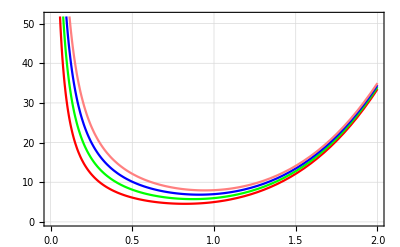

```mathematica
Plot[{c},{x,0,2},PlotStyle-> {Red,Green,Blue,Pink},
GridLines->Automatic,Frame-> True,AxesOrigin-> {0,0},PlotLegends->Automatic]
```